## Separable Initial Conditions

## Definitions

### Simple Check

```mathematica
fr[r_]:=r
fθ[θ_]:=Cos[θ]^2
fϕ[ϕ_]:=Sin[ϕ]

Uϕ0[r_,θ_,ϕ_]:=fr[r]fθ'[θ]fϕ[ϕ]
Uθ0[r_,θ_,ϕ_]:=-fr[r]fθ[θ]fϕ'[ϕ]/Sin[θ]
```

### Concentric Radial

```mathematica
(* Size/Location parameters *)
r0=13/10;
σr=1/12;
σθ=1/3;
σϕ=1/3;

rf=N[-(ⅇ^(-r0^2/(2 σr^2)) σr (r0^2+σr^2) (r0^2+8 σr^2)-√(π/2) r0 (r0^4+10 r0^2 σr^2+15 σr^4) (2-Erfc[r0/(√2 σr)]))/(ⅇ^(-r0^2/(2 σr^2)) r0 σr (r0^2+5 σr^2)+√(π/2) (r0^4+6 r0^2 σr^2+3 σr^4) (1+Erf[r0/(√2 σr)])),32];
rmax=N[Root[rf σr^2+(r0 rf-2 σr^2) #1+(-r0-rf) #1^2+#1^3&,2],32];
fru[r_]:=(rf-r)r Exp[-(r-r0)^2/(2 σr^2)];
Nr=1/fru[rmax];
fr[r_]:=Nr(rf-r)r Exp[-(r-r0)^2/(2 σr^2)];

fθ[θ_]:=Sin[θ]^2 Exp[-(θ-π/2)^2/(2 σθ^2)](*1-LegendreP[2,0,Cos[θ]]*);
fϕ[ϕ_]:=Exp[-(ϕ-π)^2/(2 σϕ^2)];

Uϕ0[r_,θ_,ϕ_]:=fr[r](fθ'[θ]fϕ[ϕ])
Uθ0[r_,θ_,ϕ_]:=-fr[r](fθ[θ]fϕ'[ϕ])/Sin[θ]
fmax=FindMaximum[√(Uθ0[r,θ,ϕ]^2+Uϕ0[r,θ,ϕ]^2),{r,r0-σr},{θ,π/2-.1`32},{ϕ,π+.01`32},WorkingPrecision->2 MachinePrecision-1][[1]]
Uϕ0[r_,θ_,ϕ_]:=fr[r](fθ'[θ]fϕ[ϕ])/fmax
Uθ0[r_,θ_,ϕ_]:=-fr[r](fθ[θ]fϕ'[ϕ])/Sin[θ]/fmax
```

2.02030095022686545438050484741

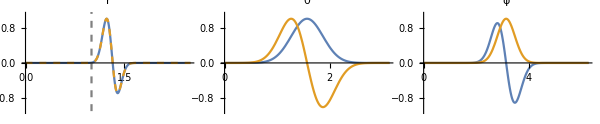

```mathematica
Show[Plot[{fr[r],fr[r]},{r,0,2.5},PlotRange->{-1.1,1.1},PlotLabel->"r",PlotStyle->{Default,Dashed}],ListPlot[{{1,-10},{1,10}},Joined->True,PlotStyle->{Dashed,Gray}]];
Plot[{fθ[θ],fθ'[θ]/fmax}//Evaluate,{θ,0,π},PlotRange->{-1.1,1.1},PlotLabel->"θ"];
Plot[{fϕ'[ϕ]/fmax,fϕ[ϕ]}//Evaluate,{ϕ,0,2π},PlotRange->{-1.1,1.1},PlotLabel->"ϕ"];
GraphicsRow[{%%%,%%,%},-5,ImageSize->600]
```

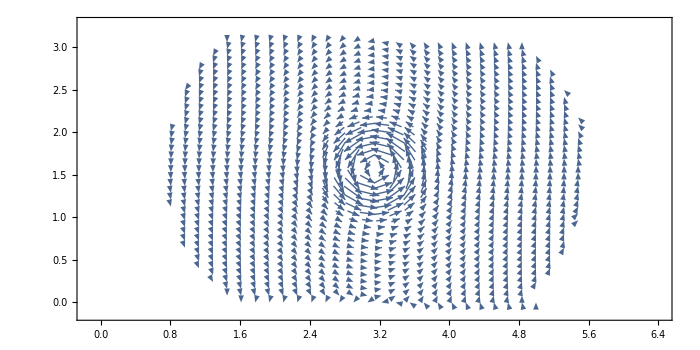

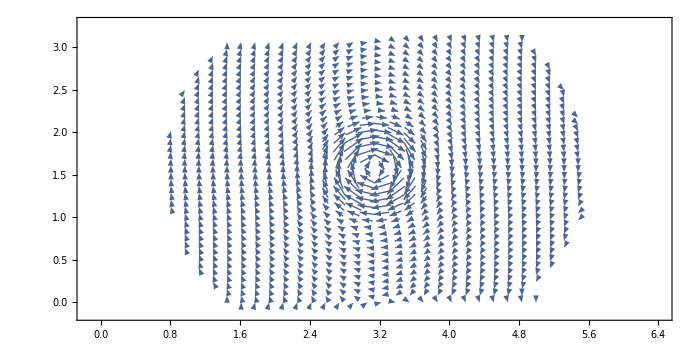

```mathematica
VectorPlot[{Uϕ0[r0-σr,θ,ϕ](*-.5Uϕ0b[r0,θ,ϕ]*),Uθ0[r0-σr,θ,ϕ](*-.5Uθ0b[r0,θ,ϕ]*)},{ϕ,0,2π-0},{θ,0,π-0},VectorScale->{.04,Automatic,Automatic},VectorPoints->40,ImageSize->700,GridLines->{{(*π+σϕb,π-σϕb,*)π+σϕ,π-σϕ},{(*π/2+σθb,π/2-σθb,*)π/2+σθ,π/2-σθ}},AspectRatio->1/2]
VectorPlot[{Uϕ0[r0+σr,θ,ϕ](*-.5Uϕ0b[r0,θ,ϕ]*),Uθ0[r0+σr,θ,ϕ](*-.5Uθ0b[r0,θ,ϕ]*)},{ϕ,0,2π-0},{θ,0,π-0},VectorScale->{.04,Automatic,Automatic},VectorPoints->40,ImageSize->700,GridLines->{{(*π+σϕb,π-σϕb,*)π+σϕ,π-σϕ},{(*π/2+σθb,π/2-σθb,*)π/2+σθ,π/2-σθ}},AspectRatio->1/2]
```

```mathematica
Plot3D[{√(Uθ0[r0-σr,θ,ϕ]^2+Uϕ0[r0-σr,θ,ϕ]^2)},{ϕ,2.,2π-2.},{θ,1.,π-1.},PlotRange->All,AspectRatio->1/2]
```

-Graphics3D-

```mathematica
FindMaximum[Uϕ0[r0,π/2,ϕ],{ϕ,3.5}]
FindMaximum[Uθ0[r0,θ,π],{θ,1.5}]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{0.,{ϕ→3.5}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{0.,{θ→1.5}}

```mathematica
FindMaximum[√(Uθ0[r,θ,ϕ]^2+Uϕ0[r,θ,ϕ]^2),{r,r0-σr},{θ,π/2+.1`32},{ϕ,π+.4`32},WorkingPrecision->2 MachinePrecision]
```

{1.,{r→1.229687188679886184611891254274,θ→1.873224048585017088462773924172,ϕ→3.141592653589793262496546853397}}

```mathematica
FindMaximum[Uϕ0[r,θ,ϕ],{r,r0-σr},{θ,π/2-.1`32},{ϕ,π+.4`32},WorkingPrecision->2 MachinePrecision]
```

{1.,{r→1.229687188679886184675020971825,θ→1.268368605004776149450094315937,ϕ→3.141592653589793238469557341113}}

### Quadrupole

```mathematica
(* initial condition *)
r0=13/10;
σr=1/12;
σθ=1/3`32;
σϕ=1/3`32;

r0a=(r0^2-σr^2)/r0;
(*Nr=2(r0a+√(r0a^2+4 σr^2))^-1 Exp[((r0a-√(r0a^2+4 σr^2))^2/(8 σr^2))];*)
fr[r_]:=(*Nr *)r Exp[-(r-r0a)^2/(2 σr^2)];
fθ[θ_]:=Evaluate[Sin[θ]^2 D[Exp[-(θ-π/2)^2/(2 σθ^2)],{θ,1(*0*)}]](*Sin[θ]^3*)(*1-LegendreP[2,0,Cos[θ]]*);
fϕ[ϕ_]:=Evaluate[D[Exp[-(ϕ-π)^2/(2 σϕ^2)],{ϕ,1}]](*1*);

Uϕ0[r_,θ_,ϕ_]:=fr[r](fθ'[θ]fϕ[ϕ])
Uθ0[r_,θ_,ϕ_]:=-fr[r](fθ[θ]fϕ'[ϕ])/Sin[θ]
fmax=FindMaximum[√(Uθ0[r0,θ,ϕ]^2+Uϕ0[r0,θ,ϕ]^2),{θ,π/2-.2`32},{ϕ,π+.4`32},WorkingPrecision->2 MachinePrecision][[1]]
Uϕ0[r_,θ_,ϕ_]:=fr[r](fθ'[θ]fϕ[ϕ])/fmax
Uθ0[r_,θ_,ϕ_]:=-fr[r](fθ[θ]fϕ'[ϕ])/Sin[θ]/fmax

(*θma=π/2-σθa;                       (* θ max *)
fθma=D[fθa[θ],θ]/.θ->θma; (* max polar dependence *)
ϕma=π-σϕa;
fϕma=D[fϕa[ϕ],ϕ]/.ϕ->ϕma;*)
(*fmaxa=Max[fθma,fϕma];
fmaxb=Max[fθmb,fϕmb];*)
```

21.24553086697893992209997933501

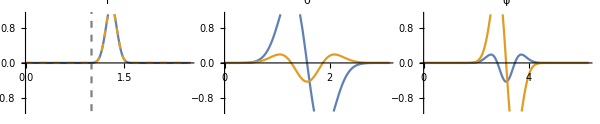

```mathematica
Show[Plot[{fr[r],fr[r]},{r,0,2.5},PlotRange->{-1.1,1.1},PlotLabel->"r",PlotStyle->{Default,Dashed}],ListPlot[{{1,-10},{1,10}},Joined->True,PlotStyle->{Dashed,Gray}]];
Plot[{fθ[θ],fθ'[θ]/fmax}//Evaluate,{θ,0,π},PlotRange->{-1.1,1.1},PlotLabel->"θ"];
Plot[{fϕ'[ϕ]/fmax,fϕ[ϕ]}//Evaluate,{ϕ,0,2π},PlotRange->{-1.1,1.1},PlotLabel->"ϕ"];
GraphicsRow[{%%%,%%,%},-5,ImageSize->600]
```

```mathematica
nf=fr[r0]//N
```

0.695057

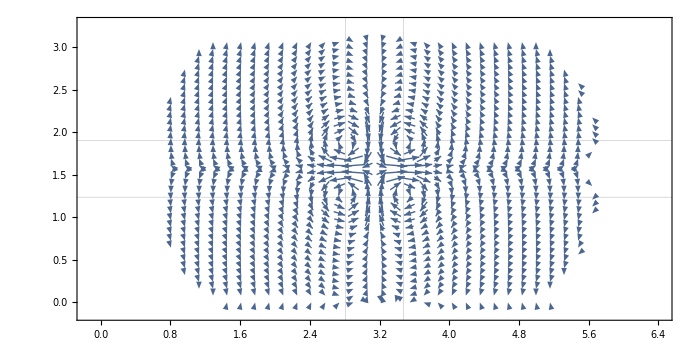

```mathematica
VectorPlot[{Uϕ0[r0,θ,ϕ](*-.5Uϕ0b[r0,θ,ϕ]*),Uθ0[r0,θ,ϕ](*-.5Uθ0b[r0,θ,ϕ]*)},{ϕ,0,2π-0},{θ,0,π-0},VectorScale->{.04,Automatic,Automatic},VectorPoints->40,ImageSize->700,GridLines->{{(*π+σϕb,π-σϕb,*)π+σϕ,π-σϕ},{(*π/2+σθb,π/2-σθb,*)π/2+σθ,π/2-σθ}},AspectRatio->1/2]
```

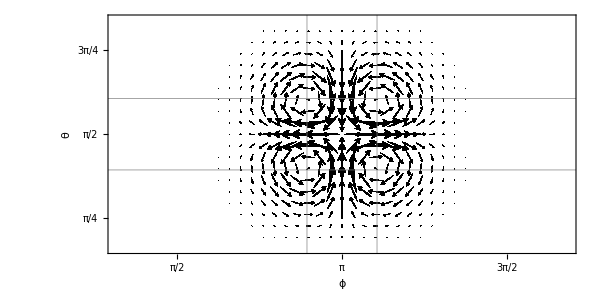

```mathematica
VectorPlot[{Uϕ0[r0,θ,ϕ](*-.5Uϕ0b[r0,θ,ϕ]*),Uθ0[r0,θ,ϕ](*-.5Uθ0b[r0,θ,ϕ]*)},{ϕ,1,2π-1},{θ,.5,π-.5},VectorScale->{.07,Automatic,Automatic},VectorPoints->{41,21},
PlotRange->{{1,2π-1},{.5,π-.5}},VectorStyle->{Black,"PinDart"},
ImageSize->600,AspectRatio->1/2,
GridLines->{{(*π+σϕb,π-σϕb,*)π+σϕ,π-σϕ},{(*π/2+σθb,π/2-σθb,*)π/2+σθ,π/2-σθ}},
GridLinesStyle->RGBColor[0.5,0.5,0.5],
LabelStyle->{Directive[Black,FontFamily->Times,FontSize->18]},
Frame->True,
FrameLabel->{"ϕ","θ"},
FrameStyle->Thickness[.003],
FrameTicks->{{{{0,"0"},{π/8,""},{π/4,"π/4",{.015,0}},{3π/8,"",{.0075,0}},{π/2,"π/2",{.015,0}},{5π/8,"",{.0075,0}},{3π/4,"3π/4",{.015,0}},{7π/8,""},{π,"π"}},{{0,""},{π/8,""},{π/4,"",{.015,0}},{3π/8,"",{.0075,0}},{π/2,"",{.015,0}},{5π/8,"",{.0075,0}},{3π/4,"",{.015,0}},{7π/8,""},{π,""}}},{{{0,"0"},{π/8,""},{π/4,"π/4",{.015,0}},{3π/8,"",{.0075,0}},{π/2,"π/2",{.015,0}},{5π/8,"",{.0075,0}},{3π/4,"3π/4",{.015,0}},{7π/8,"",{.0075,0}},{π,"π",{.015,0}},{9π/8,"",{.0075,0}},{5π/4,"5π/4",{.015,0}},{11π/8,"",{.0075,0}},{3π/2,"3π/2",{.015,0}},{13π/8,"",{.0075,0}},{7π/4,"7π/4",{.015,0}},{15π/8,""},{2π,"2π"}},{{0,""},{π/8,""},{π/4,"",{.015,0}},{3π/8,"",{.0075,0}},{π/2,"",{.015,0}},{5π/8,"",{.0075,0}},{3π/4,"",{.015,0}},{7π/8,"",{.0075,0}},{π,"",{.015,0}},{9π/8,"",{.0075,0}},{5π/4,"",{.015,0}},{11π/8,"",{.0075,0}},{3π/2,"",{.015,0}},{13π/8,"",{.0075,0}},{7π/4,"",{.015,0}},{15π/8,""},{2π,""}}}},
FrameTicksStyle->Directive[RGBColor[0,0,0],Thickness[.002]]
]
```

```mathematica
Plot3D[{√(Uθ0[r0,θ,ϕ]^2+Uϕ0[r0,θ,ϕ]^2)},{ϕ,0.,2π-0.},{θ,0.,π-0.},PlotRange->All,AspectRatio->1/2]
```

-Graphics3D-

```mathematica
FindMaximum[Uϕ0[r0,π/2,ϕ],{ϕ,3.5}]
FindMaximum[Uθ0[r0,θ,π],{θ,1.5}]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{0.,{ϕ→3.5}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{0.,{θ→1.5}}

```mathematica
FindMaximum[√(Uθ0[r0,θ,ϕ]^2+Uϕ0[r0,θ,ϕ]^2),{θ,π/2+.1`32},{ϕ,π+.4`32},WorkingPrecision->2 MachinePrecision]
```

{1.,{θ→1.570796326794896619191677865198,ϕ→3.474925986923126571802321154658}}

```mathematica
FindMaximum[Abs[Uϕ0[r0,θ,ϕ]],{θ,π/2+.1`32},{ϕ,π+.4`32},WorkingPrecision->2 MachinePrecision]
```

{0.9999999999999999999999999999995,{θ→1.570796326794896532040302636549,ϕ→3.474925986923126378897379646822}}

```mathematica
π+σϕ
```

3.47492598692312657179597671661284

## Divergence

```mathematica
D[Sin[θ](Uθ0[r,θ,ϕ]),θ]//Simplify;
D[Uϕ0[r,θ,ϕ],ϕ]//Simplify;
%+%%//Simplify
%//Chop
```

ⅇ^(-72. r^2-4.5 θ^2-4.5 ϕ^2) (ⅇ^(99.37142857142857142857142857143 r+14.13716694115406957308189522476 θ+28.27433388230813914616379044952 ϕ) r (0.+0. ϕ+0. ϕ^2+θ (0.+0. ϕ+0. ϕ^2)) Cos[θ] Sin[θ]+ⅇ^(99.37142857142857142857142857143 r+14.13716694115406957308189522476 θ+28.27433388230813914616379044952 ϕ) r (0.+0. ϕ+0. ϕ^2+θ (0.+0. ϕ+0. ϕ^2)+θ^2 (0.+0. ϕ+0. ϕ^2)) Sin[θ]^2)

0

## Angular momentum

### Simplified to one separable integral

```mathematica
rm=8;

Jx=-2 NIntegrate[fr[r]r^3,{r,0,rm}]NIntegrate[fθ[θ]Sin[θ]^2,{θ,0,π}]NIntegrate[fϕ[ϕ]Cos[ϕ],{ϕ,0,2π}]
Jy=-2 NIntegrate[fr[r]r^3,{r,0,rm}]NIntegrate[fθ[θ]Sin[θ]^2,{θ,0,π}]NIntegrate[fϕ[ϕ]Sin[ϕ],{ϕ,0,2π}]
Jz=-2 NIntegrate[fr[r]r^3,{r,0,rm}]NIntegrate[fθ[θ]Sin[θ]Cos[θ],{θ,0,π}]NIntegrate[fϕ[ϕ],{ϕ,0,2π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {3.27649}. NIntegrate obtained -3.22659×10^-16 and 2.03164×10^-16 for the integral and error estimates.

2.29778×10^-17

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {4.58957}. NIntegrate obtained 1.23165×10^-16 and 5.52727×10^-16 for the integral and error estimates.

-8.77108×10^-18

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.20259}. NIntegrate obtained 3.03577×10^-17 and 2.03165×10^-17 for the integral and error estimates.

-1.96637×10^-17

### r x u_0 -- two separable integrals

```mathematica
Jx=-NIntegrate[fr[r]r^3,{r,0,rm}]NIntegrate[fθ[θ],{θ,0,π}]NIntegrate[fϕ'[ϕ](-Sin[ϕ]),{ϕ,0,2π}]-NIntegrate[fr[r]r^3,{r,0,rm}]NIntegrate[fθ'[θ]Sin[θ]Cos[θ],{θ,0,π}]NIntegrate[fϕ[ϕ]Cos[ϕ],{ϕ,0,2π}]
Jy=-NIntegrate[fr[r]r^3,{r,0,rm}]NIntegrate[fθ[θ],{θ,0,π}]NIntegrate[fϕ'[ϕ]Cos[ϕ],{ϕ,0,2π}]-NIntegrate[fr[r]r^3,{r,0,rm}]NIntegrate[fθ'[θ]Sin[θ]Cos[θ],{θ,0,π}]NIntegrate[fϕ[ϕ]Sin[ϕ],{ϕ,0,2π}]
Jz=NIntegrate[fr[r]r^3,{r,0,rm}]NIntegrate[fθ'[θ]Sin[θ]^2,{θ,0,π}]NIntegrate[fϕ[ϕ],{ϕ,0,2π}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {3.27649}. NIntegrate obtained -3.22659×10^-16 and 2.03164×10^-16 for the integral and error estimates.

1.95935×10^-17

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {4.58957}. NIntegrate obtained 1.23165×10^-16 and 5.52727×10^-16 for the integral and error estimates.

-7.47923×10^-18

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.09828}. NIntegrate obtained 1.38778×10^-17 and 1.79405×10^-16 for the integral and error estimates.

4.49456×10^-18

### Angular Momentum of Eigenfunctions

```mathematica
Rs=1.`64;      (* stellar surface *)
c1=1;               (* internal wave speed *)
c2=580;             (* external wave speed *)
μ1=1;              (* internal shear modulus *)
μ2=1;              (* external shear modulus *)

α=(c2 μ1 -c1 μ2)/(c2 μ1 +c1 μ2)    (* reflection coefficient *)
```

579/581

```mathematica
A1[l_,ω_]=-((I Rs ω)/c2) ((1-α)SphericalBesselJ[l,(Rs ω)/c1]( (Rs ω)/ c2 SphericalHankelH1[l-1,(Rs ω)/c2]-(l+2) SphericalHankelH1[l,(Rs ω)/c2])-(1+α)SphericalHankelH1[l,(Rs ω)/c2]( (Rs ω)/ c2 SphericalBesselJ[l-1,(Rs ω)/c1]-c1/c2 (l+2) SphericalBesselJ[l,(Rs ω)/c1]));
```

```mathematica
frj[r_]=Piecewise[{{(1-α)SphericalBesselJ[l,r ω/1],0<r<1},{1/2 A1[l,ω]SphericalHankelH2[l,r ω/580],1<r}}]/.{l->1,ω->ww[1,1]};
fθj[θ_]=LegendreP[l,m,Cos[θ]]/.{l->3,m->0};
fϕj[ϕ_]=Exp[ⅈ m ϕ]/.m->0;
```

```mathematica
Jr=NIntegrate[frj[r]r^3,{r,0,4}]
Jxyθ=NIntegrate[fθj[θ]Sin[θ]^2,{θ,0,π}]
Jzθ=NIntegrate[fθj[θ]Sin[θ]Cos[θ],{θ,0,π}]
Jxϕ=NIntegrate[fϕj[ϕ]Cos[ϕ],{ϕ,0,2π}]
Jyϕ=NIntegrate[fϕj[ϕ]Sin[ϕ],{ϕ,0,2π}]
Jzϕ=NIntegrate[fϕj[ϕ],{ϕ,0,2π}]
Print["Jx"]
Jxyθ Jxϕ
Print["Jy"]
Jxyθ Jyϕ
Print["Jz"]
Jzθ Jzϕ
```

0.008552-1.1708×10^-8 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.00026}. NIntegrate obtained 8.67362×10^-18 and 5.70178×10^-17 for the integral and error estimates.

8.67362×10^-18

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.1415805607065542416335380757064221768359857378527522087097167969}. NIntegrate obtained -3.81097×10^-17 and 2.26883×10^-16 for the integral and error estimates.

-3.81097×10^-17

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {3.27649}. NIntegrate obtained -3.22659×10^-16 and 2.03164×10^-16 for the integral and error estimates.

-3.22659×10^-16

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {4.58957}. NIntegrate obtained 1.23165×10^-16 and 5.52727×10^-16 for the integral and error estimates.

1.23165×10^-16

6.28319

Jx

-2.79862×10^-33

Jy

1.06829×10^-33

Jz

-2.3945×10^-16

## Strain Energy

### Definition of tensor components

```mathematica
ethth[rr_,th_,ph_]=D[Uθ0[rr,th,ph], th]/rr;
ephph[rr_,th_,ph_]=D[Uϕ0[rr,th,ph], ph]/(rr Sin[th])+Uθ0[rr,th,ph] Cot[th]/rr;
errth[rr_,th_,ph_]=rr/2 D[(Uθ0[rr,th,ph]/rr), rr];
errph[rr_,th_,ph_]=rr/2 D[(Uϕ0[rr,th,ph]/rr), rr];
ethph[rr_,th_,ph_]=Sin[th]/(2rr)D[(Uϕ0[rr,th,ph]/Sin[th]), th]+D[Uθ0[rr,th,ph], ph]/(2 rr Sin[th]);
```

### 3-dimensional integral

```mathematica
ee=1*^-6; (* test convergence *)
wp=20;
rm=30;

(*eththint=NIntegrate[ethth[rr,th,ph]^2 rr^2 Sin[th],{rr,ee,rm},{th,ee,Pi-ee},{ph,ee,2Pi-ee},AccuracyGoal->Infinity,PrecisionGoal->12,WorkingPrecision->32,Method->{"GlobalAdaptive","MaxErrorIncreases"->500(*,Method->"GaussKronrodRule"*)}]*)(*
ephphint=NIntegrate[ephph[rr,th,ph]^2 rr^2Sin[th],{rr,ee,rm},{th,ee,Pi-ee},{ph,ee,2Pi-ee},WorkingPrecision->wp]*)
(*errthint=NIntegrate[errth[rr,th,ph]^2 rr^2Sin[th],{rr,ee,rm},{th,ee,Pi-ee},{ph,ee,2Pi-ee},WorkingPrecision->wp]*)
errphint=NIntegrate[errph[rr,th,ph]^2 rr^2Sin[th],{rr,ee,rm},{th,ee,Pi-ee},{ph,ee,2Pi-ee},WorkingPrecision->wp,AccuracyGoal->15]
(*ethphint=NIntegrate[ethph[rr,th,ph]^2 rr^2Sin[th],{rr,ee,rm},{th,ee,Pi-ee},{ph,ee,2Pi-ee},WorkingPrecision->wp]*)

Etot=eththint(*+ephphint*)+2(errthint+errphint+ethphint)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

9.4687428427670624034

21.07430595039050044

### Separable integrals

```mathematica
(* calculate integrals by separating rr th and ph components *)
eththint=NIntegrate[fr[rr]^2,{rr,0,rm},WorkingPrecision->wp]NIntegrate[Csc[th](-Cot[th] fθ[th]+fθ'[th])^2,{th,0,Pi},WorkingPrecision->wp]NIntegrate[fϕ'[ph]^2 ,{ph,0,2Pi},WorkingPrecision->wp]
ephphint=NIntegrate[fr[rr]^2,{rr,0,rm},WorkingPrecision->wp]NIntegrate[Csc[th](-Cot[th] fθ[th]+fθ'[th])^2,{th,0,Pi},WorkingPrecision->wp]NIntegrate[fϕ'[ph]^2 ,{ph,0,2Pi},WorkingPrecision->wp]
errthint=NIntegrate[(fr[rr]-rr fr'[rr])^2,{rr,0,rm},WorkingPrecision->wp]NIntegrate[1/4 Csc[th] fθ[th]^2 ,{th,0,Pi},WorkingPrecision->wp]NIntegrate[fϕ'[ph]^2 ,{ph,0,2Pi},WorkingPrecision->wp]
errphint=NIntegrate[(fr[rr]-rr fr'[rr])^2,{rr,0,rm},WorkingPrecision->wp]NIntegrate[Sin[th] fθ'[th]^2,{th,0,Pi},WorkingPrecision->wp]NIntegrate[1/4 fϕ[ph]^2 ,{ph,0,2Pi},WorkingPrecision->wp]
ethphint=NIntegrate[1/4 fr[rr]^2 ,{rr,0,rm},WorkingPrecision->wp](NIntegrate[ Sin[th] (Csc[th]^4 fθ[th]^2),{th,0,Pi},WorkingPrecision->wp]NIntegrate[fϕ''[ph]^2,{ph,0,2Pi},WorkingPrecision->wp]+NIntegrate[ Sin[th] (2 Csc[th]^2 fθ[th] (Cot[th] fθ'[th]-fθ''[th])),{th,0,Pi},WorkingPrecision->wp]NIntegrate[ (fϕ[ph] fϕ''[ph]),{ph,0,2Pi},WorkingPrecision->wp]+NIntegrate[ Sin[th] ((-Cot[th] fθ'[th]+fθ''[th])^2),{th,0,Pi},WorkingPrecision->wp]NIntegrate[fϕ[ph]^2,{ph,0,2Pi},WorkingPrecision->wp])

Etot=eththint+ephphint+2(errthint+errphint+ethphint)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

10.29238661037768657

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

1.068410132428624359

22.72159348561262186

### Reduced separable integrals

```mathematica
ϵ=10^-10;
wp=20;
rm=8;

frA=NIntegrate[(fr[r])^2,{r,0,rm},WorkingPrecision->wp]
frB=NIntegrate[(r fr'[r]-fr[r])^2,{r,0,rm},WorkingPrecision->wp]

fθA=NIntegrate[Csc[θ](fθ'[θ]-fθ[θ]Cot[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθB=NIntegrate[Csc[θ](fθ[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθC=NIntegrate[Sin[θ](fθ'[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθD=NIntegrate[Sin[θ](fθ''[θ]-fθ'[θ]Cot[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθE=NIntegrate[Csc[θ]^3(fθ[θ])^2,{θ,ϵ,π-ϵ},WorkingPrecision->wp];
fθF=NIntegrate[Csc[θ]fθ[θ](fθ''[θ]-fθ'[θ]Cot[θ]),{θ,0,π},WorkingPrecision->wp];

fϕA=NIntegrate[(fϕ'[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕB=NIntegrate[(fϕ[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕC=NIntegrate[(fϕ''[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕD=NIntegrate[fϕ[ϕ](fϕ''[ϕ]) ,{ϕ,0,2π},WorkingPrecision->wp];

ϵθθI=frA fθA fϕA
ϵϕϕI=ϵθθI
ϵrθI=1/4 frB fθB fϕA
ϵrϕI=1/4 frB fθC fϕB
ϵθϕI=1/4 frA(fθD fϕB +fθE fϕC -2fθF fϕD)
Print["
Total Strain Energy:"]
Etot=ϵθθI+ϵϕϕI+2(ϵrθI+ϵrϕI+ϵθϕI)
```

0.24808621043909970648

30.993663549081853385

286.8879312035119507

286.8879312035119507

581.3736649421411165

637.1971346389957065

105.3033610594269432

Total Strain Energy:

3221.524183688151434

## Superposition of Separable Initial Conditions

## Definitions

```mathematica
(* initial condition *)
r0=7/10;
σr=1/12;
σθa=1/3;
σϕa=1/3;
σθb=9/8 σθa ;
σϕb=9/8 σϕa;


r0a=(r0^2-σr^2)/r0;
Nr=2(r0a+√(r0a^2+4 σr^2))^-1 Exp[((r0a-√(r0a^2+4 σr^2))^2/(8 σr^2))];
fr[r_]:=Nr r Exp[-(r-r0a)^2/(2 σr^2)];

fθa[θ_]:=Sin[θ]^2 Exp[-(θ-π/2)^2/(2 σθa^2)];
fϕa[ϕ_]:=Exp[-(ϕ-π)^2/(2 σϕa^2)];
fθb[θ_]:=Sin[θ]^2 Exp[-(θ-π/2)^2/(2 σθb^2)];
fϕb[ϕ_]:=Exp[-(ϕ-π)^2/(2 σϕb^2)];

famp=N[ⅇ^(-8 σθa^2+8 σθb^2-σϕa^2/2+σϕb^2/2)(σθa σϕa (6 ⅇ^(8 σθa^2) Erf[π/(2 √2 σθa)]+4 ⅇ^(6 σθa^2) (Erf[(π-4 ⅈ σθa^2)/(2 √2 σθa)]+Erf[(π+4 ⅈ σθa^2)/(2 √2 σθa)])+Erf[(π-8 ⅈ σθa^2)/(2 √2 σθa)]+Erf[(π+8 ⅈ σθa^2)/(2 √2 σθa)]) (Erf[(π-ⅈ σϕa^2)/(√2 σϕa)]+Erf[(π+ⅈ σϕa^2)/(√2 σϕa)]))/(σθb σϕb (6 ⅇ^(8 σθb^2) Erf[π/(2 √2 σθb)]+4 ⅇ^(6 σθb^2) (Erf[(π-4 ⅈ σθb^2)/(2 √2 σθb)]+Erf[(π+4 ⅈ σθb^2)/(2 √2 σθb)])+Erf[(π-8 ⅈ σθb^2)/(2 √2 σθb)]+Erf[(π+8 ⅈ σθb^2)/(2 √2 σθb)]) (Erf[(π-ⅈ σϕb^2)/(√2 σϕb)]+Erf[(π+ⅈ σϕb^2)/(√2 σϕb)])),25]//Chop;

Uϕ0[rr_,th_,ph_]:=fr[rr](fθa'[th]fϕa[ph]-famp fθb'[th]fϕb[ph])
Uθ0[rr_,th_,ph_]:=-fr[rr](fθa[th]fϕa'[ph]-famp fθb[th]fϕb'[ph])/Sin[th]
fmax=FindMaximum[√(Uθ0[r0,θ,ϕ]^2+Uϕ0[r0,θ,ϕ]^2),{θ,π/2-.1`32},{ϕ,π+.01`32},WorkingPrecision->2 MachinePrecision][[1]];
Uϕ0[rr_,th_,ph_]:=fr[rr](fθa'[th]fϕa[ph]-famp fθb'[th]fϕb[ph])/fmax
Uθ0[rr_,th_,ph_]:=-fr[rr](fθa[th]fϕa'[ph]-famp fθb[th]fϕb'[ph])/Sin[th]/fmax
```

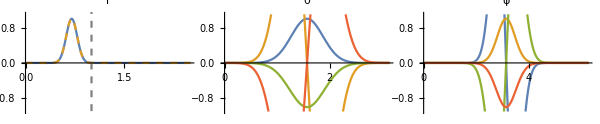

```mathematica
Show[Plot[{fr[r],fr[r]},{r,0,2.5},PlotRange->{-1.1,1.1},PlotLabel->"r",PlotStyle->{Default,Dashed}],ListPlot[{{1,-10},{1,10}},Joined->True,PlotStyle->{Dashed,Gray}]];
Plot[{fθa[θ],fθa'[θ]/fmax,-fθb[θ],-fθb'[θ]/fmax}//Evaluate,{θ,0,π},PlotRange->{-1.1,1.1},PlotLabel->"θ"];
Plot[{fϕa'[ϕ]/fmax,fϕa[ϕ],-fϕb'[ϕ]/fmax,-fϕb[ϕ]}//Evaluate,{ϕ,0,2π},PlotRange->{-1.1,1.1},PlotLabel->"ϕ"];
GraphicsRow[{%%%,%%,%},-5,ImageSize->600]
```

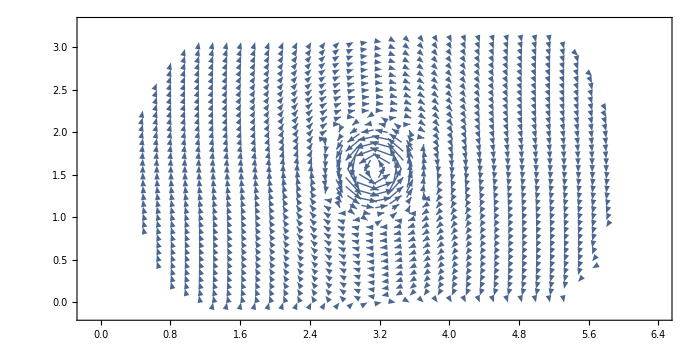

```mathematica
VectorPlot[{Uϕ0[r0,θ,ϕ](*-.5Uϕ0b[r0,θ,ϕ]*),Uθ0[r0,θ,ϕ](*-.5Uθ0b[r0,θ,ϕ]*)},{ϕ,0,2π-0},{θ,0,π-0},VectorScale->{.04,Automatic,Automatic},VectorPoints->40,ImageSize->700,GridLines->{{(*π+σϕb,π-σϕb,*)π+σϕ,π-σϕ},{(*π/2+σθb,π/2-σθb,*)π/2+σθ,π/2-σθ}},AspectRatio->1/2]
```

```mathematica
Plot3D[{√(Uθ0[r0,θ,ϕ]^2+Uϕ0[r0,θ,ϕ]^2)},{ϕ,2.,2π-2.},{θ,1.,π-1.},PlotRange->All,AspectRatio->1/2]
```

-Graphics3D-

```mathematica
FindMaximum[√(Uθ0[r0,θ,ϕ]^2+Uϕ0[r0,θ,ϕ]^2),{θ,π/2+.2`32},{ϕ,π+.1`32},WorkingPrecision->2 MachinePrecision][[1]]
```

1.

```mathematica
FindMaximum[Uϕ0[r0,θ,ϕ],{θ,π/2-.2`32},{ϕ,π+.01`32},WorkingPrecision->2 MachinePrecision][[1]]
```

0.99807939582323192480735461204

## Divergence

```mathematica
D[Sin[θ](Uθ0[r,θ,ϕ]),θ]//Simplify
D[Uϕ0[r,θ,ϕ],ϕ]//Simplify
%+%%//Simplify
%//Chop
```

-32.9491270918283074189 ⅇ^(-9/2 (16 (-1739/2520+r)^2+(-π/2+θ)^2+(π-ϕ)^2)) r Sin[θ] ((4.75605376179616628018-1.51389893160132715863 ϕ+ⅇ^(17/18 ((-π/2+θ)^2+(π-ϕ)^2)) (-3.14159265358979323846+1. ϕ)) Cos[θ]+(33.6185630058081069447-21.4022419280827482608 θ-10.7011209640413741304 ϕ+6.81254519220597221384 θ ϕ+ⅇ^(17/18 ((-π/2+θ)^2+(π-ϕ)^2)) (-17.5459633797144153224+θ (11.1701072127637092923-3.55555555555555555556 ϕ)+5.58505360638185464616 ϕ)) Sin[θ])

-32.94912709182830741888 ⅇ^(-9/2 (16 (-1739/2520+r)^2+(-π/2+θ)^2+(π-ϕ)^2)) r (π-1. ϕ) Sin[θ] ((-1.513898931601327158631+1. ⅇ^(17/18 ((-π/2+θ)^2+(π-ϕ)^2))) Cos[θ]+(-10.7011209640413741304+ⅇ^(17/18 ((-π/2+θ)^2+(π-ϕ)^2)) (5.585053606381854646156-3.555555555555555555556 θ)+6.812545192205972213839 θ) Sin[θ])

ⅇ^(-9/2 (16 (-1739/2520+r)^2+(-π/2+θ)^2+(π-ϕ)^2)) ((0. r+0. ⅇ^(17/18 ((-π/2+θ)^2+(π-ϕ)^2)) r+0. r θ+0. ⅇ^(17/18 ((-π/2+θ)^2+(π-ϕ)^2)) r θ+0. r ϕ+0. ⅇ^(17/18 ((-π/2+θ)^2+(π-ϕ)^2)) r ϕ+0. r θ ϕ+0. ⅇ^(17/18 ((-π/2+θ)^2+(π-ϕ)^2)) r θ ϕ) Sin[θ]^2+Cos[θ] (0. r Sin[θ]+0. ⅇ^(17/18 ((-π/2+θ)^2+(π-ϕ)^2)) r Sin[θ]+0. r ϕ Sin[θ]+0. ⅇ^(17/18 ((-π/2+θ)^2+(π-ϕ)^2)) r ϕ Sin[θ]))

0

## Angular momentum

```mathematica
(* using result obtained from notes *)

rm=30;

Jxa=-2 (NIntegrate[fr[r]r^3+1,{r,0,rm}]-rm)NIntegrate[fθa[θ]Sin[θ]^2,{θ,0,π}]NIntegrate[fϕa[ϕ]Cos[ϕ],{ϕ,0,2π}]
Jya=-2 (NIntegrate[fr[r]r^3+1,{r,0,rm}]-rm)NIntegrate[fθa[θ]Sin[θ]^2,{θ,0,π}](NIntegrate[fϕa[ϕ]Sin[ϕ]+1,{ϕ,0,2π}]-2π)
Jza=-2 (NIntegrate[fr[r]r^3+1,{r,0,rm}]-rm)(NIntegrate[fθa[θ]Sin[θ]Cos[θ]+1,{θ,0,π}]-π)NIntegrate[fϕa[ϕ],{ϕ,0,2π}]

Jxb=-2 (NIntegrate[fr[r]r^3+1,{r,0,rm}]-rm)NIntegrate[fθb[θ]Sin[θ]^2,{θ,0,π}]NIntegrate[fϕb[ϕ]Cos[ϕ],{ϕ,0,2π}]
Jyb=-2 (NIntegrate[fr[r]r^3+1,{r,0,rm}]-rm)NIntegrate[fθb[θ]Sin[θ]^2,{θ,0,π}](NIntegrate[fϕb[ϕ]Sin[ϕ]+1,{ϕ,0,2π}]-2π)
Jzb=-2 (NIntegrate[fr[r]r^3+1,{r,0,rm}]-rm)(NIntegrate[fθb[θ]Sin[θ]Cos[θ]+1,{θ,0,π}]-π)NIntegrate[fϕb[ϕ],{ϕ,0,2π}]

Print["Total Angular Momentum:"]
Jxa-famp Jxb
Jya-famp Jyb
Jza-famp Jzb
```

1.38912×10^-9

-1.24879×10^-23

-7.55233×10^-24

1.66162×10^-9

-1.34753×10^-23

-8.49637×10^-24

Total Angular Momentum:

-3.97047×10^-23

-1.22252×10^-24

-4.49333×10^-25

## Strain Energy

```mathematica
wp=20;
```

```mathematica
frA=NIntegrate[(fr[r])^2,{r,0,rm},WorkingPrecision->wp];
frB=NIntegrate[(r fr'[r]-fr[r])^2,{r,0,rm},WorkingPrecision->wp];

fθAa=NIntegrate[Csc[θ](fθa'[θ]-fθa[θ]Cot[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθAb=NIntegrate[Csc[θ](fθb'[θ]-fθb[θ]Cot[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθAab=NIntegrate[Csc[θ](fθa'[θ]-fθa[θ]Cot[θ])(fθb'[θ]-fθb[θ]Cot[θ]),{θ,0,π},WorkingPrecision->wp];
fθBa=NIntegrate[Csc[θ](fθa[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθBb=NIntegrate[Csc[θ](fθb[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθBab=NIntegrate[Csc[θ](fθa[θ])(fθb[θ]),{θ,0,π},WorkingPrecision->wp];
fθCa=NIntegrate[Sin[θ](fθa'[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθCb=NIntegrate[Sin[θ](fθb'[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθCab=NIntegrate[Sin[θ](fθa'[θ])(fθb'[θ]),{θ,0,π},WorkingPrecision->wp];
fθDa=NIntegrate[Sin[θ](fθa''[θ]-fθa'[θ]Cot[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθDb=NIntegrate[Sin[θ](fθb''[θ]-fθb'[θ]Cot[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθDab=NIntegrate[Sin[θ](fθa''[θ]-fθa'[θ]Cot[θ])(fθb''[θ]-fθb'[θ]Cot[θ]),{θ,0,π},WorkingPrecision->wp];
fθEa=NIntegrate[Csc[θ]^3(fθa[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθEb=NIntegrate[Csc[θ]^3(fθb[θ])^2,{θ,0,π},WorkingPrecision->wp];
fθEab=NIntegrate[Csc[θ]^3(fθa[θ])(fθb[θ]),{θ,0,π},WorkingPrecision->wp];
fθFaa=NIntegrate[Csc[θ]fθa[θ](fθa''[θ]-fθa'[θ]Cot[θ]),{θ,0,π},WorkingPrecision->wp];
fθFbb=NIntegrate[Csc[θ]fθb[θ](fθb''[θ]-fθb'[θ]Cot[θ]),{θ,0,π},WorkingPrecision->wp];
fθFab=NIntegrate[Csc[θ]fθb[θ](fθa''[θ]-fθa'[θ]Cot[θ]),{θ,0,π},WorkingPrecision->wp];
fθFba=NIntegrate[Csc[θ]fθa[θ](fθb''[θ]-fθb'[θ]Cot[θ]),{θ,0,π},WorkingPrecision->wp];

fϕAa=NIntegrate[(fϕa'[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕAb=NIntegrate[(fϕb'[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕAab=NIntegrate[(fϕa'[ϕ])(fϕb'[ϕ]) ,{ϕ,0,2π},WorkingPrecision->wp];
fϕBa=NIntegrate[(fϕa[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕBb=NIntegrate[(fϕb[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕBab=NIntegrate[(fϕa[ϕ])(fϕb[ϕ]) ,{ϕ,0,2π},WorkingPrecision->wp];
fϕCa=NIntegrate[(fϕa''[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕCb=NIntegrate[(fϕb''[ϕ])^2 ,{ϕ,0,2π},WorkingPrecision->wp];
fϕCab=NIntegrate[(fϕa''[ϕ])(fϕb''[ϕ]) ,{ϕ,0,2π},WorkingPrecision->wp];
fϕDaa=NIntegrate[fϕa[ϕ](fϕa''[ϕ]) ,{ϕ,0,2π},WorkingPrecision->wp];
fϕDbb=NIntegrate[fϕb[ϕ](fϕb''[ϕ]) ,{ϕ,0,2π},WorkingPrecision->wp];
fϕDab=NIntegrate[fϕa[ϕ](fϕb''[ϕ]) ,{ϕ,0,2π},WorkingPrecision->wp];
fϕDba=NIntegrate[fϕb[ϕ](fϕa''[ϕ]) ,{ϕ,0,2π},WorkingPrecision->wp];

ϵθθI=frA (fθAa fϕAa+famp^2 fθAb fϕAb-famp 2fθAab fϕAab)
ϵϕϕI=ϵθθI
ϵrθI=1/4 frB (fθBa fϕAa+famp^2 fθBb fϕAb-famp 2fθBab fϕAab)
ϵrϕI=1/4 frB (fθCa fϕBa+famp^2 fθCb fϕBb-famp 2fθCab fϕBab)
ϵθϕI=1/4 frA((fθDa fϕBa+famp^2 fθDb fϕBb-famp 2fθDab fϕBab)+(fθEa fϕCa+famp^2 fθEb fϕCb-famp 2fθEab fϕCab)-2fθFaa fϕDaa-famp^2 2fθFbb fϕDbb+famp 2fθFba fϕDba+famp 2fθFab fϕDab)

Etot=ϵθθI+ϵϕϕI+2(ϵrθI+ϵrϕI+ϵθϕI)
```

0.0940601026817410162

0.0940601026817410162

0.10383549685577965

0.094731069049880347

0.094433308370063722

0.77411995391492946

```mathematica
(* Evaluate θ Orthogonality Integrals *)
Do[
TH1a[l,0]=NIntegrate[√((2l+1)/(4π))D[(fθa[θ]), θ]((l+1)LegendreP[l+1,0,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,0,Cos[θ]]),{θ,0,π},AccuracyGoal->Automatic];
TH2a[l,0]=NIntegrate[√((2l+1)/(4π))fθa[θ]/Sin[θ] LegendreP[l,0,Cos[θ]],{θ,.01,π-.01},AccuracyGoal->Automatic];
TH1b[l,0]=NIntegrate[√((2l+1)/(4π))D[(fθb[θ]), θ]((l+1)LegendreP[l+1,0,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,0,Cos[θ]]),{θ,0,π},AccuracyGoal->Automatic];
TH2b[l,0]=NIntegrate[√((2l+1)/(4π))fθb[θ]/Sin[θ] LegendreP[l,0,Cos[θ]],{θ,.01,π-.01},AccuracyGoal->Automatic];

Do[
TH1a[l,m]=NIntegrate[√((2l+1)/(4π))√(((l-m)!)/((l+m)!))D[(fθa[θ]), θ]((l+1-m)LegendreP[l+1,m,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,m,Cos[θ]]),{θ,0,π},AccuracyGoal->Automatic];
TH2a[l,m]=NIntegrate[√((2l+1)/(4π))√(((l-m)!)/((l+m)!))fθa[θ]/Sin[θ] LegendreP[l,m,Cos[θ]],{θ,.01,π-.01},AccuracyGoal->Automatic];
TH1a[l,-m]=(-1)^m TH1a[l,m];
TH2a[l,-m]=(-1)^m TH2a[l,m];
TH1b[l,m]=NIntegrate[√((2l+1)/(4π))√(((l-m)!)/((l+m)!))D[(fθb[θ]), θ]((l+1-m)LegendreP[l+1,m,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,m,Cos[θ]]),{θ,0,π},AccuracyGoal->Automatic];
TH2b[l,m]=NIntegrate[√((2l+1)/(4π))√(((l-m)!)/((l+m)!))fθb[θ]/Sin[θ] LegendreP[l,m,Cos[θ]],{θ,.01,π-.01},AccuracyGoal->Automatic];
TH1b[l,-m]=(-1)^m TH1b[l,m];
TH2b[l,-m]=(-1)^m TH2b[l,m];
,{m,1,l}]
,{l,lmin,lmax}]//Timing
```

{12.2344,Null}

```mathematica
(* Evaluate ϕ Orthogonality Integrals *)
PH1a[0]=NIntegrate[fϕa[ϕ],{ϕ,0,2π}];
PH2a[0]=0;
PH1b[0]=NIntegrate[fϕb[ϕ],{ϕ,0,2π}];
PH2b[0]=0;
Do[
PH1a[m]=NIntegrate[fϕa[ϕ] Exp[-ⅈ m ϕ],{ϕ,0,2π},AccuracyGoal->Automatic];
PH2a[m]=NIntegrate[-ⅈ m D[(fϕa[ϕ]), ϕ]Exp[-ⅈ m ϕ],{ϕ,0,2π},AccuracyGoal->Automatic];

PH1a[-m]=Conjugate[PH1a[m]];
PH2a[-m]=Conjugate[PH2a[m]];

PH1b[m]=NIntegrate[fϕb[ϕ] Exp[-ⅈ m ϕ],{ϕ,0,2π},AccuracyGoal->Automatic];
PH2b[m]=NIntegrate[-ⅈ m D[(fϕb[ϕ]), ϕ]Exp[-ⅈ m ϕ],{ϕ,0,2π},AccuracyGoal->Automatic];

PH1b[-m]=Conjugate[PH1b[m]];
PH2b[-m]=Conjugate[PH2b[m]];
,{m,1,lmax}];//Timing
```

{0.296875,Null}

```mathematica
E0=Etot
```

0.77411995391492946

```mathematica
(* Sum Over just m *)
Rp=2.`16;
μ2=1;
Δt=0.02;
Do[
THPH[l]=Sum[(TH1a[l,m]PH1a[m]+TH2a[l,m]PH2a[m]-famp TH1b[l,m]PH1b[m]-famp TH2b[l,m]PH2b[m])^2,{m,-l,l}],
{l,lmin,lmax}];
Do[
EnergyFluxlrp2[l]=Table[
{10^6/10^8 Δt(t-1),
-μ2/E0 l(l+1)THPH[l](Rp^2 F2rD[l][[1,1,t]]-Rp F2aD[l][[1,1,t]])F2tD[l][[1,1,t]]/fmax^2},
{t,250000}]//Chop;
,{l,lmin,lmax}]//Timing
```

{77.6719,Null}